# Whitehead doubling.

--Jason, November 2024. The purpose of this notebook is to experiment with taking Whitehead doubles of hard unknots in an effort to create even harder unknots.

```mathematica
Exit
```

```mathematica
Needs["PM`"]
UninstallPackages[$PM,{"KnotToolsLink"}];
ClearAllCache[$PM];
LoadPackages[{"Geometries","KnotToolsLink"}]
```

Deleting package KnotToolsLink.

Deleting installation path.

Deleting files {/Users/jasoncantarella/PackageSources_2024-10-29T11-34-54/PackageSources/KnotToolsLink/PlanarDiagramObject_Library.nb}

WARNING: LTemplate has not yet been tested with Mathematica 14.1.0.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

Updating package KnotToolsLink...

/Users/jasoncantarella/PackageSources_2024-10-29T11-34-54/PackageSources/KnotToolsLink/LibrarySources/PlanarDiagramObject/

Exporting library PlanarDiagramObject to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source.

Names of functions in library PlanarDiagramObject are made public.

Current directory is: /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/Source

Unloading library PlanarDiagramObject ...

Generating library code ...

Compiling library code ...

Compilation done. Time elapsed = 22.5785

```mathematica
hardknotfiles=FileNames[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","diagrams","hardunknots","*.tsv"}]];
```

```mathematica
culprit = PlanarDiagram[Import[hardknotfiles[[1]]]]
```

PlanarDiagramObject[…]

```mathematica
PlotDiagram[culprit]
```

-Graphics-

```mathematica
ClearAll[ReginaAdditiveR1];ReginaAdditiveR1[{pd_,k_,σ_}]:= Module[{time,res},
ReginaSetLink[pd];
time=AbsoluteTiming[res = ExternalEvaluate[
$knotpython,
"regina_L.r1(regina_L.strand("<>IntegerString[k]<>"),0,"<>IntegerString[σ]<>");"
];][[1]];
PlanarDiagram[ReginaGetLink[]]
]
```

```mathematica
PlotDiagram[ReginaAdditiveR1[{culprit,1,-1}]]
```

0.399113 s elapsed while compiling PDCodeAppendSign.

Writing to /Users/jasoncantarella/Library/Wolfram/Applications/KnotToolsLink/LibraryResources/MacOSX-ARM64/PDCodeAppendSign.dylib.

-Graphics-

We’re also going to want to compute linking numbers:

```mathematica
ClearAll[ReginaLinkingNumber]; ReginaLinkingNumber[pd_]:=
Module[{time,res},
ReginaSetLink[pd];
time=AbsoluteTiming[res = ExternalEvaluate[
$knotpython,
"regina_L.linking();"
];][[1]];
res
]
```

```mathematica
ClearAll[ReginaWrithe]; ReginaWrithe[pd_]:=
Module[{time,res},
ReginaSetLink[pd];
time=AbsoluteTiming[res = ExternalEvaluate[
$knotpython,
"regina_L.writhe();"
];][[1]];
res
]
```

And take parallel cables:

```mathematica
ClearAll[ReginaBlackboardCable];ReginaBlackboardCable=PackageFunction[{pd_,k_},
Module[{},
ReginaSetLink[pd];
ExternalEvaluate[
$knotpython,
"par_L = regina_L.parallel("<>IntegerString[k]<>",framing=regina.Framing(2));\nregina_L = par_L;"
];
PlanarDiagram[ReginaGetLink[]]
]
]
```

```mathematica
ReginaLinkingNumber[ReginaBlackboardCable[culprit,2]]
```

2

```mathematica
ClearAll[ReginaSelfFrame];ReginaSelfFrame=PackageFunction[{pd_},
Module[{},
ReginaSetLink[pd];
ExternalEvaluate[
$knotpython,
"regina_L.selfFrame()"
];
PlanarDiagram[ReginaGetLink[]]
]
]
```

Now we’re going to try to reverse one component of the link. Let’s look at some pictures of crossings in a PD code to understand how to write this combinatorially

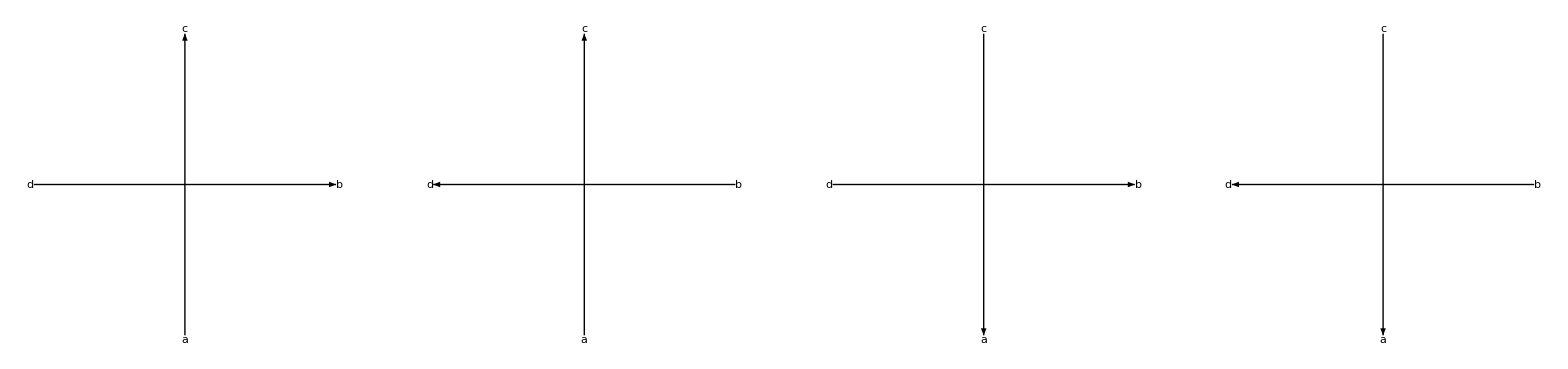

```mathematica
Block[{up,down,left,right,labels},
up ={{0,-1},{0,1}}; down = -up;
right = {{-1,0},{1,0}}; left = -right;
labels ={ Text["a",up[[1]],{Center,Top}],
Text["b",left[[1]],{Left,Center}],
Text["c",down[[1]],{Center,Bottom}],
Text["d",right[[1]],{Right,Center}]};
GraphicsGrid[
{{Graphics[{Arrow/@{up,right},labels},PlotRangePadding->Scaled[.1]],
Graphics[{Arrow/@{up,left},labels},PlotRangePadding->Scaled[.1]],
Graphics[{Arrow/@{down,right},labels},PlotRangePadding->Scaled[.1]],
Graphics[{Arrow /@ {down,left},labels},PlotRangePadding->Scaled[.1]]}}
]
]
```

We see from this that we really only care if arcs a and c are part of the reversed component. If so, we must swap a and c (because now c is incoming and a is outgoing) and ALSO swap b and d (because now d is the counterclockwise neighbor of the incoming arc). Otherwise, we do nothing (since we don’t know whether b and d are going left or right anyway). The understrand and overstrand don’t change.

```mathematica
ClearAll[ReverseComponent]; ReverseComponent[pd_,k_]:= Block[{c,p},
c = LinkComponentArcs[pd][[k]];
(*Echo[PDCode[pd]];*)
p = 
(If[SubsetQ[c,#[[{1,3}]]],
#[[{3,4,1,2}]],
#[[{1,2,3,4}]]
]&) /@PDCode[pd];
 PlanarDiagram[PDCodeAppendSign/@(p /. Rule@@@Transpose[{c,Reverse[c]}])]
]
```

Now we’re prepared to start work on the Whitehead double. This is going to be a bit fiddly. Here’s the strategy. First, we ensure that the original diagram has nonzero writhe by adding an R1. Then we self-frame. After this, we have zero writhe. When we resolve one of the twists to make a clasp, we’ll have an extra twist (of the opposite sign). We find it and take it out. The resulting diagram should be the Whitehead double with an extra Unlink. We then modify the unlink count.

We first come up with some code which filters out the four crossings in the rectangle adjacent to an R1 loop:

```mathematica
ClearAll[BuildR1Squares];BuildR1Squares[crcr_]:=Block[{a,b,c,d},
Table[
{{a,b},{c,d}} = crcr[[k]];
If[b ==d ==k-1,{{a,k-1},{crcr[[a+1,1,1]],c}},
If[a == c==k-1,{{d,k-1},{crcr[[d+1,2,2]],b}},
Nothing],
Nothing
],
{k,1,Length[crcr]}
]
]
```

```mathematica
ClearAll[WhiteheadDouble]; WhiteheadDouble[pd_]:= Module[{pd2,newP,crcr,σ,claspSquare,killSquare,lastP},
σ=If[#==0,+1,#]&@Sign[ReginaWrithe[pd]];
pd2 = ReginaSelfFrame[ReginaAdditiveR1[{pd,1,σ}]];
newP = ReverseComponent[ReginaBlackboardCable[pd2,2],1];
crcr=CrossingCrossings[newP];
{claspSquare,killSquare} =SelectFirst[
Subsets[BuildR1Squares[crcr],{2}],CrossingState[newP,#[[1,1,1]]] != CrossingState[newP,#[[2,1,1]]]&];

ResolveCrossing[newP,claspSquare[[1,1]]];
SwitchCrossing[newP,claspSquare[[2,2]]];

ResolveCrossing[newP,killSquare[[2,1]]];
ResolveCrossing[newP,killSquare[[2,2]]];
SwitchCrossing[newP,killSquare[[1,1]]];

CompressDiagramInPlace[newP];
lastP = SimplifyDiagram4[newP];
CompressDiagramInPlace[lastP];
lastP
]
```

```mathematica
PlotDiagram[culprit]
```

-Graphics-

```mathematica
PlotDiagram[weirdP = WhiteheadDouble[culprit]]
```

-Graphics-

```mathematica
ReginaHOMFLY[weirdP]
```

Function[{L,M},1]

```mathematica
Rattle[weirdP,1]
```

{PlanarDiagramObject[…]}

And, since nobody can leave well-enough alone:

```mathematica
weirderP = Nest[WhiteheadDouble,culprit,4]
```

PlanarDiagramObject[…]

```mathematica
trial = Rattle[weirderP,10]
```

{PlanarDiagramObject[…]}

```mathematica
PlotDiagram[SimplifyDiagram4[trial[[1]]]]
```

-Graphics-

```mathematica
Rattle[trial[[1]],1]
```

{PlanarDiagramObject[…]}